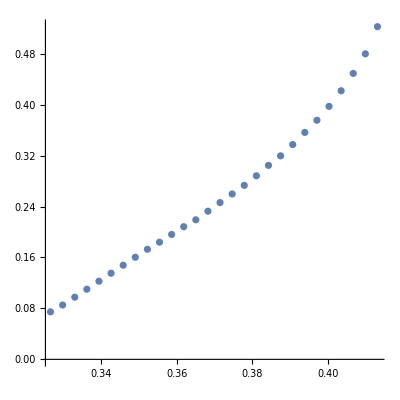

```mathematica
v1=1;
bat16=Import["C:\\Users\\renan\\Desktop\\new\\576\\xp2\\stages\\xls\\BAT16.xls"];
d16=11.74;
h16=31.23;
fTAV16=Table[{bat16[[i]][[1]]*9.81 (* F[N] *),N[(i-1)/10] (* t[s] *),(Pi/4)*d16^2 (* A[mm^2]*),v1 (* v[mm/s] *)},{i,1,Length[bat16]}];
deltaSt16=Table[{fTAV16[[i]][[2]]fTAV16[[i]][[4]],fTAV16[[i]][[1]]/fTAV16[[i]][[3]]},{i,1,Length[bat16]}];
strainStress16=Table[{deltaSt16[[i]][[1]]/h16,deltaSt16[[i]][[2]]},{i,1,Length[bat16]}];
strainStressFit16=Table[{deltaSt16[[i]][[1]]/h16,deltaSt16[[i]][[2]]},{i,103,130}];
g16=ListPlot[strainStress16,PlotStyle->{Blue,PointSize[.007]}];
ListPlot[strainStressFit16,AspectRatio->1]
```

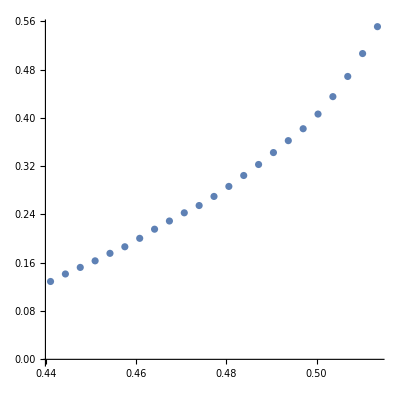

```mathematica
bat17=Import["C:\\Users\\renan\\Desktop\\new\\576\\xp2\\stages\\xls\\BAT17.xls"];
d17=11.12;
h17=30.38;
fTAV17=Table[{bat17[[i]][[1]]*9.81 (* F[N] *),N[(i-1)/10] (* t[s] *),(Pi/4)*d17^2 (* A[mm^2]*),v1 (* v[mm/s] *)},{i,1,Length[bat17]}];
deltaSt17=Table[{fTAV17[[i]][[2]]fTAV17[[i]][[4]],fTAV17[[i]][[1]]/fTAV17[[i]][[3]]},{i,1,Length[bat17]}];
strainStress17=Table[{deltaSt17[[i]][[1]]/h17,deltaSt17[[i]][[2]]},{i,1,Length[bat17]}];
strainStressFit17=Table[{deltaSt17[[i]][[1]]/h17,deltaSt17[[i]][[2]]},{i,135,157}];
g17=ListPlot[strainStress17,PlotStyle->{Green,PointSize[.007]}];
ListPlot[strainStressFit17,AspectRatio->1]
```

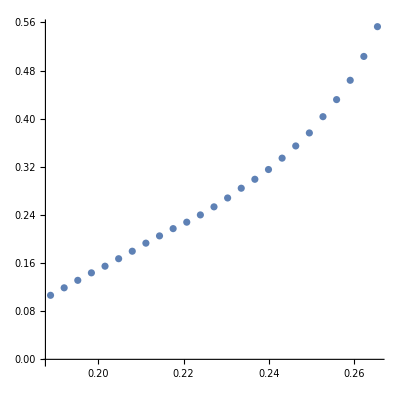

```mathematica
bat18=Import["C:\\Users\\renan\\Desktop\\new\\576\\xp2\\stages\\xls\\BAT18.xls"];
d18=11.79;
h18=31.26;
fTAV18=Table[{bat18[[i]][[1]]*9.81 (* F[N] *),N[(i-1)/10] (* t[s] *),(Pi/4)*d18^2 (* A[mm^2]*),v1 (* v[mm/s] *)},{i,1,Length[bat18]}];
deltaSt18=Table[{fTAV18[[i]][[2]]fTAV18[[i]][[4]],fTAV18[[i]][[1]]/fTAV18[[i]][[3]]},{i,1,Length[bat18]}];
strainStress18=Table[{deltaSt18[[i]][[1]]/h18,deltaSt18[[i]][[2]]},{i,1,Length[bat18]}];
strainStressFit18=Table[{deltaSt18[[i]][[1]]/h18,deltaSt18[[i]][[2]]},{i,60,Length[bat18]-32}];
g18=ListPlot[strainStress18,PlotStyle->{Magenta,PointSize[.007]}];
ListPlot[strainStressFit18,AspectRatio->1]
```

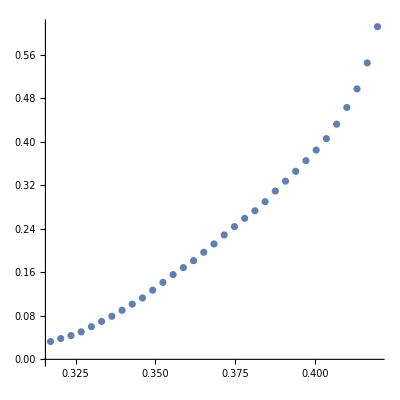

```mathematica
bat19=Import["C:\\Users\\renan\\Desktop\\new\\576\\xp2\\stages\\xls\\BAT19.xls"];
d19=11.6;
h19=31.22;
fTAV19=Table[{bat19[[i]][[1]]*9.81 (* F[N] *),N[(i-1)/10] (* t[s] *),(Pi/4)*d19^2 (* A[mm^2]*),v1 (* v[mm/s] *)},{i,1,Length[bat19]}];
deltaSt19=Table[{fTAV19[[i]][[2]]fTAV19[[i]][[4]],fTAV19[[i]][[1]]/fTAV19[[i]][[3]]},{i,1,Length[bat19]}];
strainStress19=Table[{deltaSt19[[i]][[1]]/h19,deltaSt19[[i]][[2]]},{i,1,Length[bat19]}];
strainStressFit19=Table[{deltaSt19[[i]][[1]]/h19,deltaSt19[[i]][[2]]},{i,100,Length[bat19]-28}];
g19=ListPlot[strainStress19,PlotStyle->{Red,PointSize[.007]}];
ListPlot[strainStressFit19,AspectRatio->1]
```

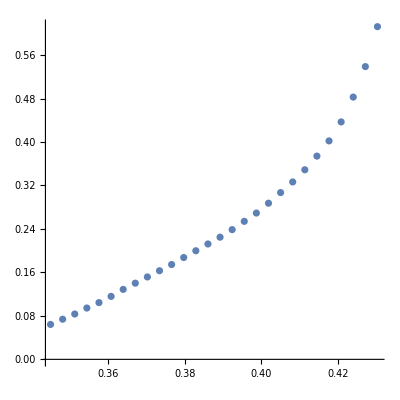

```mathematica
bat20=Import["C:\\Users\\renan\\Desktop\\new\\576\\xp2\\stages\\xls\\BAT20.xls"];
d20=11.59;
h20=31.6;
fTAV20=Table[{bat20[[i]][[1]]*9.81 (* F[N] *),N[(i-1)/10] (* t[s] *),(Pi/4)*d20^2 (* A[mm^2]*),v1 (* v[mm/s] *)},{i,1,Length[bat20]}];
deltaSt20=Table[{fTAV20[[i]][[2]]fTAV20[[i]][[4]],fTAV20[[i]][[1]]/fTAV20[[i]][[3]]},{i,1,Length[bat20]}];
strainStress20=Table[{deltaSt20[[i]][[1]]/h20,deltaSt20[[i]][[2]]},{i,1,Length[bat20]}];
strainStressFit20=Table[{deltaSt20[[i]][[1]]/h20,deltaSt20[[i]][[2]]},{i,110,Length[bat20]-32}];
g20=ListPlot[strainStress20,PlotStyle->{Purple,PointSize[.007]}];
ListPlot[strainStressFit20,AspectRatio->1]
```

```mathematica
line16 = Fit[strainStressFit16, {1,x},x];
line17 = Fit[strainStressFit17, {1,x},x];
line18 = Fit[strainStressFit18, {1,x},x];
line19 = Fit[strainStressFit19, {1,x},x];
line20 = Fit[strainStressFit20, {1,x},x];
```

```mathematica
xp1={{.5,3.22},{.8,3.54},{1.2,3.77}};
```

```mathematica
f[x_]:=2.864729729729731+0.7743243243243234 x
```

```mathematica
m=(line16[[2]][[1]]+line17[[2]][[1]]+line18[[2]][[1]]+line19[[2]][[1]]+line20[[2]][[1]])/5
```

5.14215

```mathematica
e1=f[1]
```

3.63905

```mathematica
Solve[m==(e1(1-v))/((1+v)(1-2v)),v ]
```

{{v→-0.4623},{v→0.316146}}

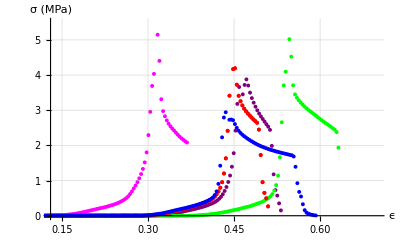

```mathematica
Show[ContourPlot[y==10,{x,0.13,.7},{y,0,5.5}],g19,g20,g18,g17,g19,g16,AspectRatio->.6,GridLines->Automatic,GridLinesStyle->Directive[LightGray, Dashed],Axes->True,Frame->False,AxesLabel->{"ϵ","σ (MPa)"}]
```